```mathematica
ClearSystemCache[];
ClearAll["Global`*"];
<<NumericalDifferentialEquationAnalysis`
```

#### Optical properties

#### Matrix size

```mathematica
M=32;
```

#### Albedo

```mathematica
a=0.9;
```

#### Optical thickness

```mathematica
τ=1.0;
```

#### Anisotropy

```mathematica
g=0.9;
```

#### Refractive index

```mathematica
n=1.4;
nglass=1.56;
```

### Integrating spheres properties

#### Distance from spheres to tissue

```mathematica
z=3.5×10^-3;
```

#### Sphere diameter

```mathematica
d=7.×10^-3;
r=d/2;
```

#### Quadrature angles

Total internal reflection

```mathematica
θ [n_]= ArcSin[1.0/n];
```

Critical cosine

```mathematica
νc[n_]=Cos[θ[n]];
```

Gauss (0<θ<ν_c)

```mathematica
gauss=GaussianQuadratureWeights[M/2,0,νc[n]];
νGauss=gauss[[All,1]];
wGauss=gauss[[All,2]];
```

Radau (ν_c<θ<1)

```mathematica
cachedLegendreP[k_,x_]:=cachedLegendreP[k,x]=LegendreP[k,x];
```

```mathematica
Radau[x_,m_]=(cachedLegendreP[m/2-1,x]+cachedLegendreP[m/2,x])/(1+x);
```

```mathematica
Der[x_,m_]=D[cachedLegendreP[m/2,x],x];
```

```mathematica
RadauRoots=Sort[Flatten[Chop[N[{x/.Solve[Radau[x,M]==0,x], -1}]]],Greater];
```

```mathematica
νRadau=Table[N[(1+νc[n])/2-(1-νc[n])/2×RadauRoots[[j]]],{j,M/2}];
```

```mathematica
wRadau=Flatten[{Table[(1-νc[n])/(2 (1-RadauRoots[[j]]) (Der[RadauRoots[[j]],M-2])^2),{j,M/2-1}],{(1-νc[n])/(M/2)^2}}];
```

#### Final quadrature angles and weights

```mathematica
ν=Flatten[{νGauss,νRadau}];
w = Flatten[{wGauss,wRadau}];
ClearAll[RadauRoots,GaussLRoots,νGauss,νRadau,wGauss,wRadau];
```

```mathematica
anglesRad=Table[ArcCos[ν[[i]]],{i,Length[ν]}];
anglesDeg=Table[(anglesRad[[i]] 180)/π,{i,Length[ν]}]
```

{89.7875,88.8887,87.305,85.09,82.3157,79.0674,75.4404,71.5378,67.4695,63.3546,59.3229,55.5186,52.1016,49.2443,47.1204,45.8814,45.4487,44.8705,43.839,42.3688,40.4801,38.1981,35.5517,32.573,29.2959,25.7555,21.9877,18.028,13.9107,9.66602,5.30472,0.}

```mathematica
tanAnglesDeg=Table[Tan[anglesRad[[i]] ],{i,Length[ν]}]
```

{269.62,51.5508,21.2443,11.6406,7.41141,5.17705,3.8502,2.99524,2.41059,1.99301,1.68572,1.45602,1.28463,1.16032,1.0769,1.03125,1.01579,0.99549,0.960274,0.912127,0.85348,0.786868,0.714656,0.638863,0.561079,0.482462,0.403777,0.32546,0.247672,0.170323,0.0928503,0.}

```mathematica
distances=Table[3.5/tanAnglesDeg[[i]] ,{i,Length[ν]}]
```

Power::infy: Infinite expression 1/0. encountered.

{0.0129812,0.0678942,0.16475,0.300671,0.472245,0.676061,0.909045,1.16852,1.45193,1.75614,2.07626,2.40381,2.72452,3.0164,3.25007,3.39393,3.4456,3.51586,3.64479,3.83718,4.10086,4.44802,4.89746,5.47849,6.23798,7.25446,8.66815,10.754,14.1316,20.5492,37.6951,ComplexInfinity}

### The Redistribution Function

#### δ-M method

```mathematica
τs[A_,T_,G_]:=τs[A,T,G]=(1-A G^M)T
```

```mathematica
as[A_,G_]:=as[A,G]=A(1-G^M)/(1-A×G^M)
```

Optical thickness of starting layer: Δτ^*<ν_1 (min ν)

We want Δτ^*×2^n1=τ^*

```mathematica
n1Delayed[A_,T_,G_]:=n1Delayed[A,T,G]=Module[{myN},myN=0;While[myN<100000,If[τs[A,T,G]<Min[ν]×2^myN,Break[]];myN++];myN];
n1[A_,T_,G_]:=n1[A,T,G]=If[NumberQ[A]∧NumberQ[T]∧NumberQ[G],n1Delayed[A,T,G],HoldForm[n1[A,T,G]]];
n1[a,τ,g]
```

9

```mathematica
Δτs[A_,T_,G_]:=Δτs[A,T,G]=τs[A,T,G]/2^n1[A,T,G];
```

```mathematica
Δτ[A_,T_,G_]:=Δτ[A,T,G]=Δτs[A,T,G]/(1-A×G^M);
```

#### Heyney-Greenstein phase function

```mathematica
SuperStar[χ][k_,G_]:=SuperStar[χ][k,G]=(G^k-G^M)/(1-G^M);
```

```mathematica
PPmatrix=ConstantArray[0.,{M, M}];
PPmatrix[[1,All]]=1.;
PPmatrix[[2,All]]=ν;
Do[Do[PPmatrix[[nn,j]]=((2nn-3) ν[[j]] PPmatrix[[nn-1,j]]-(nn-2) PPmatrix[[nn-2,j]])/(nn-1),{nn,3,M}],{j,M}];
PNmatrix=Table[(-1)^(nn-1) PPmatrix[[nn,j]],{nn,1,M},{j,1,M}];
```

```mathematica
hpp[G_]:=hpp[G]=Module[{newHPP,i,j,k},newHPP=ConstantArray[0.,{M, M}];If[g==0,newHPP=ConstantArray[1.,{M, M}],Do[Do[newHPP[[i,j]]=Sum[(2k+1) SuperStar[χ][k,G]PPmatrix[[k+1,i]] PPmatrix[[k+1,j]],{k,0,M-1}],{j,i,M}],{i,M}];
Do[Do[newHPP[[j,i]]=newHPP[[i,j]],{j,i+1,M}],{i,M}]];newHPP];
hpm[G_]:=hpm[G]=Module[{newHPM,i,j,k},newHPM=ConstantArray[0.,{M, M}];If[g==0,newHPM=ConstantArray[1.,{M, M}],Do[Do[newHPM[[i,j]]=Sum[(2k+1) SuperStar[χ][k,G]PPmatrix[[k+1,i]] PNmatrix[[k+1,j]],{k,0,M-1}],{j,i,M}],{i,M}];
Do[Do[newHPM[[j,i]]=newHPM[[i,j]],{j,i+1,M}],{i,M}]];newHPM];
```

```mathematica
hpp[g];
```

```mathematica
(*ClearAll[cachedLegendreP,PPmatrix,PNmatrix];*)
```

#### Layer Initialiation

```mathematica
EE=IdentityMatrix[M];
```

```mathematica
BB[A_,T_,G_]:=BB[A,T,G]=Table[(as[A,G]×Δτs[A,T,G]×w[[j]])/(4 ν[[i]]) hpm[G][[i,j]],{i,M},{j,M}];
```

```mathematica
AA[A_,T_,G_]:=AA[A,T,G]=Table[i,j Δτs[A,T,G]/(2 ν[[i]])-(as[A,G]×Δτs[A,T,G] w[[j]])/(4 ν[[i]])hpp[G][[i,j]],{i,M},{j,M}];
```

```mathematica
Inv[A_,T_,G_]:=Inv[A,T,G]=Inverse[EE+AA[A,T,G]];
```

```mathematica
GG[A_,T_,G_]:=GG[A,T,G]=Inverse[EE+AA[A,T,G]-BB[A,T,G].Inv[A,T,G].BB[A,T,G]];
```

```mathematica
RR[A_,T_,G_]:=RR[A,T,G]=2.GG[A,T,G].BB[A,T,G].Inv[A,T,G];
```

```mathematica
TT[A_,T_,G_]:=TT[A,T,G]=2.GG[A,T,G]-EE;
```

```mathematica
(*ClearAll[A,B,G,Inv,hpp,hpm];*)
```

```mathematica
twoaw=2 ν w;
```

```mathematica
Rd1[A_,T_,G_]:=Rd1[A,T,G]=Table[(RR[A,T,G][[i,j]])/twoaw[[j]],{i,M},{j,M}];
Td1[A_,T_,G_]:=Td1[A,T,G]=Table[(TT[A,T,G][[i,j]])/twoaw[[j]],{i,M},{j,M}];
```

#### Doubling until desired thickness is reached

```mathematica
newE=DiagonalMatrix[1./twoaw];
star=DiagonalMatrix[twoaw];
```

Now I’ll try to avoid recursion here...

```mathematica
Td2=ConstantArray[0.,{M,M}];
Rd2=ConstantArray[0.,{M,M}];
Td[A_,T_,G_]:=Td[A,T,G]=Table[Td1[A,T,G],{i,n1[A,T,G]+1}];
Rd[A_,T_,G_]:=Rd[A,T,G]=Table[Rd1[A,T,G],{i,n1[A,T,G]+1}];
```

```mathematica
makeTChain[A_,T_,G_]:=makeTChain[A,T,G]=Module[{i,Tchain,Rchain},Tchain=Table[Td1[A,T,G],{i,n1[A,T,G]+1}];Rchain=Table[Rd1[A,T,G],{i,n1[A,T,G]+1}];
For[i=1,i≤n1[A,T,G],i++,
Tchain[[i+1]]=Tchain[[i]].Inverse[newE-Rchain[[i]].star.Rchain[[i]]].Tchain[[i]];
Rchain[[i+1]]=Tchain[[i]].Inverse[newE-Rchain[[i]].star.Rchain[[i]]].Rchain[[i]].star.Tchain[[i]]+Rchain[[i]]
];Tchain];
makeRChain[A_,T_,G_]:=makeRChain[A,T,G]=Module[{i,Tchain,Rchain},Tchain=Table[Td1[A,T,G],{i,n1[A,T,G]+1}];Rchain=Table[Rd1[A,T,G],{i,n1[A,T,G]+1}];
For[i=1,i≤n1[A,T,G],i++,
Tchain[[i+1]]=Tchain[[i]].Inverse[newE-Rchain[[i]].star.Rchain[[i]]].Tchain[[i]];
Rchain[[i+1]]=Tchain[[i]].Inverse[newE-Rchain[[i]].star.Rchain[[i]]].Rchain[[i]].star.Tchain[[i]]+Rchain[[i]]
];Rchain];
```

R and T for desired optical thickness

```mathematica
Rslab[A_,T_,G_]:=Rslab[A,T,G]=makeRChain[A,T,G][[n1[A,T,G]+1]];
Tslab[A_,T_,G_]:=Tslab[A,T,G]=makeTChain[A,T,G][[n1[A,T,G]+1]];
```

#### Fresnel reflection & boundary conditions

```mathematica
νt[ni_,nt_,νi_]=√(1-(ni/nt)^2 (1-νi^2));
FresnelR[νi_,ni_,nt_]=1/2 ((nt νi-ni Re[νt[ni,nt,νi]])/(nt νi+ni Re[νt[ni,nt,νi]]))^2+1/2 ((ni νi-nt Re[νt[ni,nt,νi]])/(ni νi+nt Re[νt[ni,nt,νi]]))^2;
Rbound=DiagonalMatrix[Re[Chop[((FresnelR[ν,n,nglass]+FresnelR[νt[n,nglass,ν],nglass,1]-2×FresnelR[ν,n,nglass]×FresnelR[νt[n,nglass,ν],nglass,1])/(1-FresnelR[ν,n,nglass]×FresnelR[νt[n,nglass,ν],nglass,1]))× twoaw]]];
Tbound=DiagonalMatrix[Re[Chop[1-(FresnelR[ν,n,nglass]+FresnelR[νt[n,nglass,ν],nglass,1]-2×FresnelR[ν,n,nglass]×FresnelR[νt[n,nglass,ν],nglass,1])/(1-FresnelR[ν,n,nglass]×FresnelR[νt[n,nglass,ν],nglass,1])]]];
```

#### Adding boundaries to the slab

```mathematica
T02[A_,T_,G_]:=T02[A,T,G]=Tslab[A,T,G].Inverse[EE-Rbound.Rslab[A,T,G]].Tbound;
R20[A_,T_,G_]:=R20[A,T,G]=Tslab[A,T,G].Inverse[EE-Rbound.Rslab[A,T,G]].Rbound.Tslab[A,T,G]+Rslab[A,T,G];
```

```mathematica
T03[A_?NumericQ,T_?NumericQ,G_?NumericQ]:=T03[A,T,G]=Module[{newT03},newT03=ConstantArray[0,{M,M}];If[A==0||T==0,newT03=Re[Chop[Tbound.Inverse[EE].T02[A,T,G]]],newT03=Re[Chop[Tbound.Inverse[EE-R20[A,T,G].Rbound].T02[A,T,G]]]];newT03];

R30[A_?NumericQ,T_?NumericQ,G_?NumericQ]:=R30[A,T,G]=Module[{newR30},newR30=ConstantArray[0,{M,M}];If[A==0||T==0,newR30=Re[Chop[Tbound.Inverse[EE].R20[A,T,G].Tbound]],newR30=Re[Chop[Tbound.Inverse[EE-R20[A,T,G].Rbound].R20[A,T,G].Tbound]]];newR30];
```

```mathematica
modifyR30[A_?NumericQ,T_?NumericQ,G_?NumericQ]:=modifyR30[A,T,G]=Module[{newR30,i},newR30=R30[A,T,G];For[i=1,i≤M,i++,newR30[[i,i]]+=Rbound[[i,i]]/twoaw[[i]]^2];newR30];
modifyR30[a,τ,g];
modifyR30[a,τ,g][[M]];
```

```mathematica
(*For[i=1,i≤M,i++,R30[A,T][[i,i]]+=Rbound[[i,i]]/twoaw[[i]]^2];*)
```

```mathematica
Sum[2×ν[[i]]×w[[i]]×modifyR30[a,τ,g][[M,i]],{i,1,M-2}]
```

0.0360547

#### Find total R and T

```mathematica
Rc[A_?NumericQ,T_?NumericQ,G_?NumericQ]:=Rc[A,T,G]=Total[2 ν w×modifyR30[A,T,G][[M]]];
Tc[A_?NumericQ,T_?NumericQ,G_?NumericQ]:=Tc[A,T,G]=Total[2 ν w T03[A,T,G][[M]]];
```

```mathematica
{Rc[a,τ,g],Tc[a,τ,g]}
```

{0.0998247,0.759021}

```mathematica
ν[[1]]
```

0.0037089

```mathematica
Rlist[A_?NumericQ,T_?NumericQ,G_?NumericQ]:=Rlist[A,T,G]=2 ν w×modifyR30[A,T,G][[M]];
Tlist[A_?NumericQ,T_?NumericQ,G_?NumericQ]:=Tlist[A,T,G]=2 ν w×T03[A,T,G][[M]]
```

```mathematica
Sum[Rlist[a,τ,g][[i]],{i,M-1}]
```

0.0415157

```mathematica
Sum[2 ν w×modifyR30[a,τ,g][[M]][[i]],{i,M}]
```

{0.00185361,0.0222234,0.0823544,0.19634,0.368184,0.590494,0.844916,1.10428,1.33615,1.50731,1.58852,1.55886,1.40908,1.14344,0.779703,0.347914,0.160029,0.370289,0.575042,0.769409,0.947399,1.10166,1.22383,1.30522,1.33774,1.31501,1.23334,1.09258,0.896647,0.653553,0.37494,0.0616705}

#### Find light cones within border

```mathematica
angleBorder[Z_]=N[ArcTan[r/Z]]×180/Pi;
withinBorder[Z_,list_]:=Module[{j},j=1;While[anglesDeg[[j]]>angleBorder[Z],j++];Drop[list,j-2]];
anglesWB[Z_]:=Module[{list},If[Z==0,list=anglesDeg,list=withinBorder[Z,anglesDeg]];list];
```

```mathematica
zRef[Z_]:=Z+70×10^-3;
angleBorderRef[Z_]:=N[ArcTan[r/zRef[Z]]]×180/Pi;
anglesWBRef[Z_]:=Module[{list},j=1;While[anglesDeg[[j]]>angleBorderRef[Z],j++];list=Drop[anglesDeg,j-2];list];
```

```mathematica
anglesWBRef[0.0]
```

{5.30472,0.}

#### Sum concerning only angles within border

```mathematica
RlastWB[A_?NumericQ,T_?NumericQ,G_?NumericQ,Z_?NumericQ]:=RlastWB[A,T,G,Z]=Module[{list},If[Z==0,list=R30[A,T,G][[All,M]],list=withinBorder[Z,R30[A,T,G][[All,M]]]];list];
νWB[Z_]:=νWB[Z]=Module[{list},If[Z==0,list=ν,list=withinBorder[Z,ν]];list];
wWB[Z_]:=wWB[Z]=Module[{list},If[Z==0,list=w,list=withinBorder[Z,w]];list];
R30WB[A_?NumericQ,T_?NumericQ,G_?NumericQ,Z_?NumericQ]:=R30WB[A,T,G,Z]=Transpose[{RlastWB[A,T,G,Z],νWB[Z],wWB[Z]}];
```

```mathematica
TlastWB[A_?NumericQ,T_?NumericQ,G_?NumericQ,Z_?NumericQ]:=TlastWB[A,T,G,Z]=Module[{list},If[Z==0,list=T03[A,T,G][[All,M]],list=withinBorder[Z,T03[A,T,G][[All,M]]]];list];
T03WB[A_?NumericQ,T_?NumericQ,G_?NumericQ,Z_?NumericQ]:=T03WB[A,T,G,Z]=Transpose[{TlastWB[A,T,G,Z],νWB[Z],wWB[Z]}];
```

```mathematica
RcWB[A_?NumericQ,T_?NumericQ,G_?NumericQ,Z_?NumericQ]:=RcWB[A,T,G,Z]=Sum[Chop[2×R30WB[A,T,G,Z][[i,1]]×R30WB[A,T,G,Z][[i,2]]×R30WB[A,T,G,Z][[i,3]]],{i,1,Length[R30WB[A,T,G,Z]]-1}]
TcWB[A_?NumericQ,T_?NumericQ,G_?NumericQ,Z_?NumericQ]:=TcWB[A,T,G,Z]=Sum[Chop[2×T03WB[A,T,G,Z][[i,1]]×T03WB[A,T,G,Z][[i,2]]×T03WB[A,T,G,Z][[i,3]]],{i,1,Length[R30WB[A,T,G,Z]]}]
```

```mathematica
RvsZ=ConstantArray[0,{10,2}];
TvsZ=ConstantArray[0,{10,2}];
For[i=1,i≤10,i++,RvsZ[[i,1]]=(i-1)×0.004+0.001;RvsZ[[i,2]]=RcWB[a,τ,g,(i-1)×0.004]];
For[i=1,i≤10,i++,TvsZ[[i,1]]=(i-1)×0.004+0.001;TvsZ[[i,2]]=TcWB[a,τ,g,(i-1)×0.004]];
```

```mathematica
TcWB[a,τ,g,0]
```

0.759021

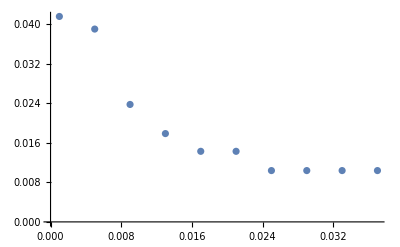

```mathematica
ListPlot[RvsZ]
```

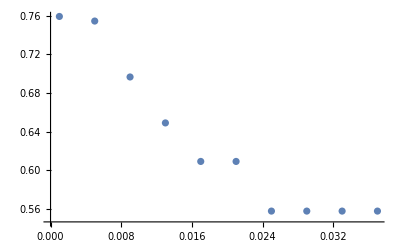

```mathematica
ListPlot[TvsZ]
```

#### Inverse problem function

```mathematica
(*Rm=0.1485;
Tm=0.4996;
Clear[MM];
MM[A_?NumericQ,T_?NumericQ,G_?NumericQ,Z_?NumericQ,Rm_?NumericQ,Tm_?NumericQ]:=MM[A,T,G,Z,Rm,Tm]=Re[Abs[RcWB[A,T,G,Z]-Rm]/(Rm+10^-6)+Abs[TcWB[A,T,G,Z]-Tm]/(Tm+10^-6)];
Results=NMinimize[{MM[A,T,G,0.0],0.9<A<1,0<T,0.7<G<1},{A,T,G},Method->{"NelderMead"}]
finalA=A/.Last[Results];
finalT=T/.Last[Results];
(*finalG=G/.Last[Results];*)
dTissue=1.049×10^-3;
μs[A_?NumericQ,T_?NumericQ]:=μs[A,T]=T/dTissue×A
μa[A_?NumericQ,T_?NumericQ]:=μa[A,T]=T/dTissue×(1-A)
finalG*)
```

```mathematica
dataR=Import["C:\\Users\\tatki\\Documents\\PHOTONICS\\Biophotonics\\Integrating spheres\\25.02.20 Milk\\PvsLL1.dat","Data"];
dataT=Import["C:\\Users\\tatki\\Documents\\PHOTONICS\\Biophotonics\\Integrating spheres\\25.02.20 Milk\\PvsLU1.dat","Data"];
dataR[[All,1]]=dataR[[All,1]]×0.001;
dataT[[All,1]]=dataT[[All,1]]×0.001;
dTissue=1.094×10^-3;
```

```mathematica
dataR
```

{{0.,0.14849},{0.004,0.0504464},{0.008,0.0270338},{0.012,0.0153002},{0.016,0.0102184},{0.02,0.00700751},{0.024,0.00544163},{0.028,0.00418942},{0.032,0.00358485},{0.036,0.00306788}}

```mathematica
ResultsTable=ConstantArray[0,{Length[dataR],3}];
MM[A_?NumericQ,T_?NumericQ,G_?NumericQ,Z_?NumericQ,Rm_?NumericQ,Tm_?NumericQ]:=MM[A,T,G,Z,Rm,Tm]=Re[Abs[RcWB[A,T,G,Z]-Rm]/(Rm+10^-6)+Abs[TcWB[A,T,G,Z]-Tm]/(Tm+10^-6)];
μs[A_?NumericQ,T_?NumericQ]:=μs[A,T]=T/dTissue×A;
μa[A_?NumericQ,T_?NumericQ]:=μa[A,T]=T/dTissue×(1-A);
```

```mathematica
(*NMinimize[{MM[A, T, G, 0.0, dataR[[1, 2]], dataT[[1, 2]]], 0.9 < A < 1, 0 < T, 0.7 < G < 1 }, {A, T, G}, Method -> {"NelderMead"}]*)
```

First row: z = 0

```mathematica
Results0=NMinimize[{MM[A, T, G, 0.0, dataR[[1, 2]], dataT[[1, 2]]], 0.9 < A < 1, 0 < T, 0.7 < G < 1 }, {A, T, G}, Method -> {"NelderMead"}];
```

```mathematica
ResultsTable[[1, 1]]=μs[(A/.Last[Results0]), (T/.Last[Results0])];ResultsTable[[1, 2]]=μa[(A/.Last[Results0]), (T/.Last[Results0])]; ResultsTable[[1,3]]=NumberForm[G/.Last[Results0],3];
```

```mathematica
ResultsTable
```

{{1973.89,119.997,0.702},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0}}

Next rows: z!=0

```mathematica
MM[a,τ, G/.Last[Results0], 0.004, dataR[[2, 2]], dataT[[2, 2]]]
```

2.28438

```mathematica
For[i=2,i≤6,i++,Results=NMinimize[{MM[A, T, G, 0.004×(i-1), dataR[[i, 2]], dataT[[i, 2]]], 0.9 < A < 1, 0 < T, 0.7 < G < 1}, {A, T, G}, Method -> {"NelderMead"}]; ResultsTable[[i, 1]]=μs[(A/.Last[Results]), (T/.Last[Results])];ResultsTable[[i, 2]]=μa[(A/.Last[Results]), (T/.Last[Results])]; ResultsTable[[i, 3]]= (G/.Last[Results]);ClearAll[Results]];
```

NMinimize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

$Aborted

```mathematica
ResultsTable//MatrixForm
```

(1973.89 | 119.997 | 0.702
5835.73 | 502.134 | 0.883474
4803.47 | 484.78 | 0.83156
5871.63 | 438.725 | 0.869817
5173.12 | 414.689 | 0.852849
5269.75 | 580.863 | 0.856327
1973.89 | 119.997 | 0.702
1973.89 | 119.997 | 0.702
1973.89 | 119.997 | 0.702
1973.89 | 119.997 | 0.702)

```mathematica
NMinimize[{MM[A, T, G, 0, dataR[[1, 2]], dataT[[1, 2]]], 0.9 < A < 1, 0 < T, 0.7 < G < 1}, {A, T, G}, Method -> {"NelderMead"}]
```

{2.72263×10^-8,{A→0.942691,T→2.29071,G→0.701723}}

```mathematica
NMinimize[{MM[A, T, G, 0.004, dataR[[2, 2]], dataT[[2, 2]]], 0.9 < A < 1, 0 < T, 0.7 < G < 1}, {A, T, G}, Method -> {"NelderMead"}]
```

{3.08556×10^-9,{A→0.920772,T→6.93363,G→0.883474}}

```mathematica
NMinimize[{MM[A, T, G, 0.008, dataR[[3, 2]], dataT[[3, 2]]], 0.9 < A < 1, 0 < T, 0.7 < G < 1}, {A, T, G}, Method -> {"NelderMead"}]
```

NMinimize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

{1.58874×10^-8,{A→0.908329,T→5.78535,G→0.83156}}

```mathematica
NMinimize[{MM[A, T, G, 0.012, dataR[[4, 2]], dataT[[4, 2]]], 0.9 < A < 1, 0 < T, 0.7 < G < 1}, {A, T, G}, Method -> {"NelderMead"}]
```

{1.11272×10^-8,{A→0.930475,T→6.90353,G→0.869817}}

```mathematica
NMinimize[{MM[A, T, G, 0.016, dataR[[5, 2]], dataT[[5, 2]]], 0.9 < A < 1, 0 < T, 0.7 < G < 1}, {A, T, G}, Method -> {"NelderMead"}]
```

{1.28607×10^-9,{A→0.925787,T→6.11306,G→0.852849}}

```mathematica
NMinimize[{MM[A, T, G, 0.02, dataR[[6, 2]], dataT[[6, 2]]], 0.9 < A < 1, 0 < T, 0.7 < G < 1}, {A, T, G}, Method -> {"NelderMead"}]
```

{1.85619×10^-9,{A→0.900718,T→6.40057,G→0.856327}}

```mathematica
ResultsTable//MatrixForm
```

(1973.89 | 119.997 | 0.702
1973.89 | 119.997 | 0.702
1973.89 | 119.997 | 0.702
1973.89 | 119.997 | 0.702
1973.89 | 119.997 | 0.702
1973.89 | 119.997 | 0.702
1973.89 | 119.997 | 0.702
1973.89 | 119.997 | 0.702
1973.89 | 119.997 | 0.702
1973.89 | 119.997 | 0.702)